```mathematica
(*Sedat Ekinci*)
<<NeuralNets`
```

```mathematica
trainingData=ExampleData[{"MachineLearning","FisherIris"},"TrainingData"];testData=ExampleData[{"MachineLearning","FisherIris"},"TestData"];
x=#[[1]]&/@trainingData

y=(#[[2]]/. {"setosa"->{1,0,0},"versicolor"->{0,1,0},"virginica"->{0,0,1}})&/@trainingData
```

{{4.7,3.2,1.3,0.2},{4.6,3.1,1.5,0.2},{5.,3.6,1.4,0.2},{5.4,3.9,1.7,0.4},{5.,3.4,1.5,0.2},{4.9,3.1,1.5,0.1},{5.4,3.7,1.5,0.2},{4.8,3.4,1.6,0.2},{4.8,3.,1.4,0.1},{5.7,4.4,1.5,0.4},{5.4,3.9,1.3,0.4},{5.4,3.4,1.7,0.2},{5.1,3.7,1.5,0.4},{4.6,3.6,1.,0.2},{5.1,3.3,1.7,0.5},{4.8,3.4,1.9,0.2},{5.,3.,1.6,0.2},{5.,3.4,1.6,0.4},{5.2,3.5,1.5,0.2},{4.7,3.2,1.6,0.2},{4.8,3.1,1.6,0.2},{5.4,3.4,1.5,0.4},{5.2,4.1,1.5,0.1},{4.9,3.1,1.5,0.2},{5.,3.2,1.2,0.2},{5.5,3.5,1.3,0.2},{4.9,3.6,1.4,0.1},{4.4,3.,1.3,0.2},{5.,3.5,1.3,0.3},{4.4,3.2,1.3,0.2},{5.,3.5,1.6,0.6},{5.1,3.8,1.9,0.4},{4.6,3.2,1.4,0.2},{5.3,3.7,1.5,0.2},{5.,3.3,1.4,0.2},{7.,3.2,4.7,1.4},{6.4,3.2,4.5,1.5},{6.9,3.1,4.9,1.5},{5.5,2.3,4.,1.3},{6.5,2.8,4.6,1.5},{6.3,3.3,4.7,1.6},{4.9,2.4,3.3,1.},{6.6,2.9,4.6,1.3},{5.2,2.7,3.9,1.4},{5.9,3.,4.2,1.5},{6.,2.2,4.,1.},{6.7,3.1,4.4,1.4},{5.6,3.,4.5,1.5},{5.6,2.5,3.9,1.1},{6.3,2.5,4.9,1.5},{6.1,2.8,4.7,1.2},{6.6,3.,4.4,1.4},{6.8,2.8,4.8,1.4},{6.7,3.,5.,1.7},{5.7,2.6,3.5,1.},{5.5,2.4,3.8,1.1},{5.5,2.4,3.7,1.},{5.8,2.7,3.9,1.2},{6.,2.7,5.1,1.6},{6.7,3.1,4.7,1.5},{6.3,2.3,4.4,1.3},{5.6,3.,4.1,1.3},{5.5,2.5,4.,1.3},{5.5,2.6,4.4,1.2},{6.1,3.,4.6,1.4},{5.8,2.6,4.,1.2},{5.,2.3,3.3,1.},{5.7,2.9,4.2,1.3},{5.1,2.5,3.,1.1},{5.7,2.8,4.1,1.3},{5.8,2.7,5.1,1.9},{6.3,2.9,5.6,1.8},{4.9,2.5,4.5,1.7},{7.3,2.9,6.3,1.8},{6.7,2.5,5.8,1.8},{7.2,3.6,6.1,2.5},{6.5,3.2,5.1,2.},{6.4,2.7,5.3,1.9},{6.8,3.,5.5,2.1},{5.7,2.5,5.,2.},{5.8,2.8,5.1,2.4},{6.5,3.,5.5,1.8},{7.7,2.6,6.9,2.3},{6.,2.2,5.,1.5},{5.6,2.8,4.9,2.},{7.7,2.8,6.7,2.},{6.3,2.7,4.9,1.8},{6.7,3.3,5.7,2.1},{6.2,2.8,4.8,1.8},{6.1,3.,4.9,1.8},{6.3,2.8,5.1,1.5},{6.1,2.6,5.6,1.4},{7.7,3.,6.1,2.3},{6.4,3.1,5.5,1.8},{6.,3.,4.8,1.8},{6.9,3.1,5.4,2.1},{6.7,3.1,5.6,2.4},{6.9,3.1,5.1,2.3},{5.8,2.7,5.1,1.9},{6.8,3.2,5.9,2.3},{6.7,3.,5.2,2.3},{6.3,2.5,5.,1.9},{6.5,3.,5.2,2.},{6.2,3.4,5.4,2.3},{5.9,3.,5.1,1.8}}

{{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1}}

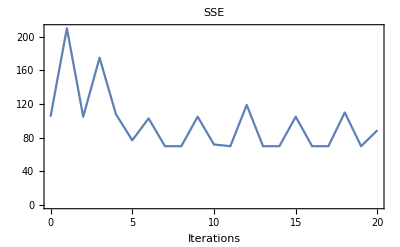

PerceptronFit::NotConverged: No solution found. The problem may not be linearly separable or you may need more iterations.

```mathematica
{per,fitrecord}=PerceptronFit[x,y, 20];
```

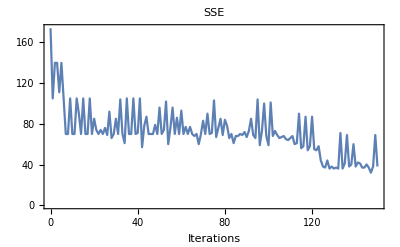

PerceptronFit::NotConverged: No solution found. The problem may not be linearly separable or you may need more iterations.

```mathematica
{per,fitrecord}=PerceptronFit[x,y, 150];
```

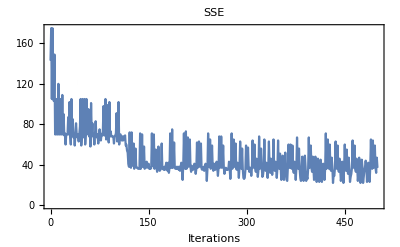

PerceptronFit::NotConverged: No solution found. The problem may not be linearly separable or you may need more iterations.

```mathematica
{per,fitrecord}=PerceptronFit[x,y, 500];
```

```mathematica
(*Even though i've tried adding more iterations to the data there is no solution found. So the data we have is not linearly seperable. Thus we can not use Perceptron for this data. If a data set is linearly separable the Perceptron will find a separating hyperplane in a finite number of updates. If the data is not linearly separable, it will loop forever*)
```